```mathematica
(*--- Biophysical model of reverse blebbing: Interacting blebs ---*)
(*--- Modified on 22/11/2021 ---*)
Clear[γM,ΤC,R0,r0,P0,rm,rE,αC,b,τ0,t1,t2,ρ,PlysV,PlysC,InflateTwoGVs,ta];

SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];
date=DateString[{"Year","_","Month","_","Day"}];
If[DirectoryQ[date]==False,CreateDirectory[date]];
SetDirectory[date];
SetOptions[Style,FontFamily->"Arial"];

(*--- Setting for figures ---*)
Size=20;imgSize=600;imagePadding={{100,100},{80,10}};
dashsty=Directive[Dashed,AbsoluteThickness[1]];
mdefault=Directive[Black,AbsoluteThickness[2]];
cdefault=Directive[Darker[RGBColor[0,154,0,255]],AbsoluteThickness[2]];
bfont=Directive[Size,Black,FontFamily->"Arial"];
rfont=Directive[Size,Darker[Red],FontFamily->"Arial"];
SetOptions[Plot,PlotRange->All];
SetOptions[ListPlot,PlotRange->All,Joined->True];
SetOptions[ListLogPlot,PlotRange->All,Joined->True];

(*--- Dynamical model ---*)
(*--- Generate inverse bleb dynamics ---*)
(*--- Fixed parameters ---*)
(*--- 1. Membrane surface tension (pN/μm) ---*)
γM=40;
(*--- 2 Cell cortex surface tension (rest state) (pN/μm) ---*)
ΤC=374;
(*--- 3.1 Initial cell radius (μm) ---*)
(*--- Realistic values: 14-35 μm ---*)
R0=10.0;
(*--- 3.2 Initial intracellular pressure (pN/μm^2) ---*)
P0=2(γM+ΤC)/R0;
(*--- 4. Pore radius (μm) ---*)
(*--- Realistic values: 1-3 μm ---*)
rm=0.25;
(*--- 5. Effective radius (μm) ---*)
(*--- Realistic values: ~10 μm ---*)
rE=10.;
(*--- 6. Reservoir size ---*)
(*--- Realistic values: 1%-30%  ---*)
αC=0.5;
(*--- 7. Stretching strength ---*)
(*--- Realistic values: (1-2)10^5 pN/μm ---*)
b=1.0 10^5;
(*--- 8. Tension relaxation timescales (s) ---*)
τ0=1; τM=0.000001;
(*--- 9. Membrane drag coefficient (s^-1) ---*)
ν0=2.5 10^4;
(*--- 10. Conversion factor Pa -> μm ---*)
cf=0.0075;

(*--- 13. Lysis tension ---*)
 Α0=3π (R0)^2-π (rE)^2; s0=π (rE)^2;
(*--- Realistic values: 2-5% ---*)
αl=0.05;
sC=π (rE)^2(1+αC); sM=(1+αl)sC; PlysV=γM+ΤC+b(Exp[(sM-sC)/sC]-1); 
ΑC=(3π R0^2-π (rE)^2)(1+αC); aM=(1+αl)ΑC; PlysC=γM+ΤC+b(Exp[(aM-ΑC)/ΑC]-1);

(*--- 15. Time sampling vector ---*)
linspace[a_,b_,d_]:=Range[a,b,d];
t1=0;t2=60 60;Δt=0.05;
ρ=linspace[t1,t2,Δt];

(*--- Two blebs case ---*)
(*--- Dynamical equations ---*)
InflateTwoGVs[p_,t0_,rV01_,rV02_,rC0_,a_,d_,ΓV0_,ΓC0_]:={
(*--- Initial conditions ---*)
r1[t0]==rV01,r2[t0]==rV02,σ[t0]==ΓC0,Σ1[t0]==ΓV0,Σ2[t0]==ΓV0,
(*--- Surface tensions ---*)
(*--- eq. 1: Cell ---*)
σ'[t]==1/λ[t](σL[t]-σ[t]),
(*--- eq. 2: Inverse blebs ---*)
Σ1'[t]==1/ξ[t](ΣL[t]-Σ1[t]),
Σ2'[t]==1/ξ[t](ΣL[t]-Σ2[t]),
(*--- eq. 3: Inverse bleb radii ---*)
(*--- Bleb 1 ---*)
F1[t]==(p-(2σ[t])/R[t]-(2Σ1[t])/r1[t]),
r1'[t]==r1[t]/(4ν0)F1[t],
(*--- Bleb 2 ---*)
F2[t]==(p-(2σ[t])/R[t]-(2Σ2[t])/r2[t]),
r2'[t]==r2[t]/(4ν0)F2[t],
(*--- other specs: additional functions ---*)
(*--- eq 4: Cell radius ---*)
R[t]==((rC0)^3+2(r1[t])^3(2+Cos[θ1[t]])(Sin[θ1[t]/2])^4+2(r2[t])^3(2+Cos[θ2[t]])(Sin[θ2[t]/2])^4)^(1/3),
(*--- eq 5: Inverse blebs opening angle ---*)
θ1[t]==(π-ArcSin[a/r1[t]]),
θ2[t]==(π-ArcSin[a/r2[t]]),
(*--- eq 6.1: Limit surface tension of the cell ---*)
Α[t]==3π (R[t])^2-π (d)^2,
σL[t]==(γM+ΤC)((1-s2[t])/2)+(γM+ΤC+b( Exp[(Α[t]-ΑC)/ΑC]-1))((1+s2[t])/2),
(*--- eq 6.2: Limit surface tension of the inverse bleb ---*)
s[t]==2π(r1[t])^2(1-Cos[θ1[t]])+2π(r2[t])^2(1-Cos[θ2[t]])+π(d^2-2 a^2),
ΣL[t]==(γM+ΤC)((1-s1[t])/2)+(γM+ΤC+b( Exp[(s[t]-sC)/sC]-1))((1+s1[t])/2),
(*--- eq 7: Tensional timescales ---*)
ξ[t]==τ0((1-s1[t])/2)+τM((1+s1[t])/2),
λ[t]==τ0((1-s2[t])/2)+τM((1+s2[t])/2),
(*--- other specs: special events ---*)
(*--- 1. Inverse bleb area expansion ---*)
s1[t0]==-1,
WhenEvent[s[t]-sC>0,s1[t]->"DiscontinuitySignature"],
(*--- 2. Cell area expansion ---*)
s2[t0]==-1,
WhenEvent[Α[t]-ΑC>0,s2[t]->"DiscontinuitySignature"],
(*--- 2. Dealing with behaviour at hemisphere ---*)
WhenEvent[r1[t]-a<10^-6,{ta=t,"StopIntegration"},
"DetectionMethod"->"Interpolation","LocationMethod"->"BrentBracketRoot"],
WhenEvent[r2[t]-a<10^-6,{ta=t,"StopIntegration"},
"DetectionMethod"->"Interpolation","LocationMethod"->"BrentBracketRoot"]
};
vars={r1[t],r2[t],R[t],θ1[t],θ2[t],σ[t],Σ1[t],Σ2[t],F1[t],F2[t],s1[t],s2[t]};
```

```mathematica
(*--- Numerical solution ---*)
Δp=7.0/cf; T=20 60;
r0=RandomVariate[UniformDistribution[{0.97351,1.2 0.97351}],2];
sol=NDSolve[InflateTwoGVs[Δp,0,r0[[1]],r0[[2]],R0,rm,rE,γM,γM+ΤC],vars,{t,0,T},DiscreteVariables->{s1[t]∈{-1,1},s2[t]∈{-1,1}},
PrecisionGoal->Infinity,AccuracyGoal->3,MaxStepSize->0.001];
Print[sol];Print[StringJoin["deflation time=",ToString[ta]]];

x1[t_]:=Evaluate[{r1[t]}]/.sol;
x2[t_]:=Evaluate[{r2[t]}]/.sol;
rC[t_]:=Evaluate[{R[t]}]/.sol;
ϕ1[t_]:=Evaluate[{θ1[t]}]/.sol;
ϕ2[t_]:=Evaluate[{θ2[t]}]/.sol;
V1[t_]:=4/3 π x1[t]^3(2+Cos[ϕ1[t]])(Sin[ϕ1[t]/2])^4;
V2[t_]:=4/3 π x2[t]^3(2+Cos[ϕ2[t]])(Sin[ϕ2[t]/2])^4;
y1[t_]:=Evaluate[{σ[t]}]/.sol;
z1[t_]:=Evaluate[{Σ1[t]}]/.sol;
z2[t_]:=Evaluate[{Σ2[t]}]/.sol;
P1[t_]:=(2y1[t])/R1[t];
f1[t]:=Evaluate[{F1[t]}]/.sol;
f2[t]:=Evaluate[{F2[t]}]/.sol;
```

{{r1[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],r2[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],R[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],θ1[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],θ2[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],σ[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],Σ1[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],Σ2[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],F1[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],F2[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],s1[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t],s2[t]→InterpolatingFunction[{{0., 1081.46}}, <>][t]}}

deflation time=1081.46

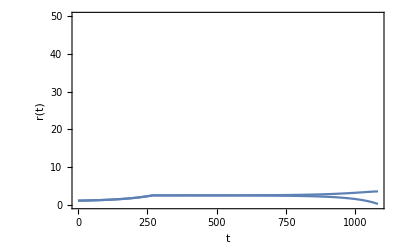

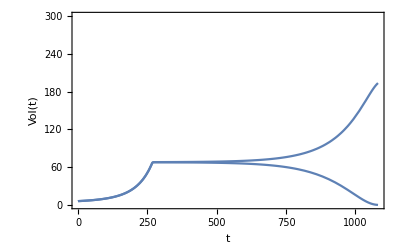

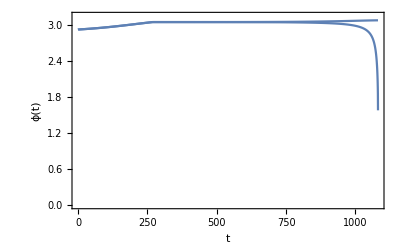

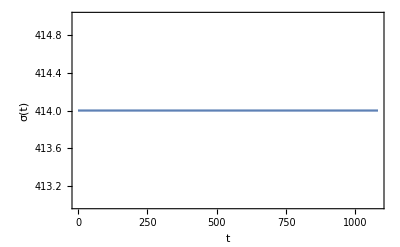

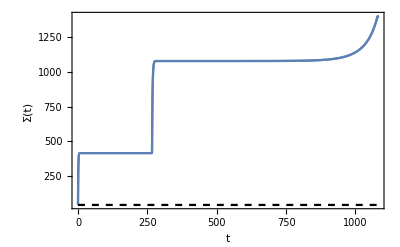

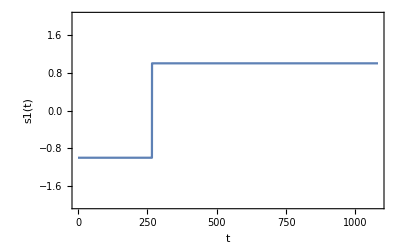

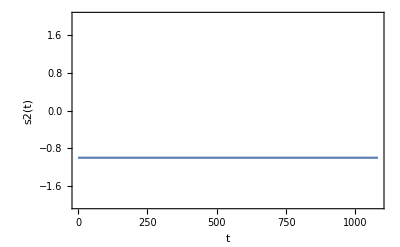

```mathematica
(*--- Check ODEs' solutions ---*)
T=ta;
(*--- a. r(t) ---*)
Show[Plot[x1[t],{t,0,T}],
Plot[x2[t],{t,0,T}],
(*Plot[rVst,{t,0,T},PlotStyle->{Dashed,Black}],*)
PlotRange->{All,{0,50}},Axes->False,Frame->{{True,False},{True,False}},
FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["r(t)",bfont]}
]
(*--- b. vol(t) ---*)
Show[Plot[V1[t],{t,0,T}],
Plot[V2[t],{t,0,T}],
(*Plot[Vst,{t,0,T},PlotStyle->{Dashed,Black}],*)
PlotRange->{All,{0,300}},Axes->False,Frame->{{True,False},{True,False}},
FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["Vol(t)",bfont]}
]
(*--- b. ϕ(t) ---*)
Show[Plot[ϕ1[t],{t,0,T},PlotRange->{All,{0,π}}],
Plot[ϕ2[t],{t,0,T},PlotRange->{All,{0,π}}],
(*Plot[ϕst,{t,0,T},PlotStyle->{Dashed,Black}],*)
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["ϕ(t)",bfont]}
]
(*--- a. σ(t) ---*)
Show[Plot[y1[t],{t,0,T},PlotRange->All],
(*Plot[σst,{t,0,T},PlotStyle->{Dashed,Black}],
Plot[σ0,{t,0,T},PlotStyle->{Dashed,Black}],*)
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["σ(t)",bfont]}
]
(*--- a. Σ(t) ---*)
Show[Plot[z1[t],{t,0,T},PlotRange->All],
Plot[z2[t],{t,0,T},PlotRange->All],
(*Plot[σst,{t,0,T},PlotStyle->{Dashed,Black}],*)
Plot[γM,{t,0,T},PlotStyle->{Dashed,Black}],
(*Plot[σ0,{t,0,T},PlotStyle->{Dashed,Black}],*)
Axes->False,Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["Σ(t)",bfont]}
]

Plot[Evaluate[{s1[t]}]/.sol,{t,0,T},PlotRange->{All,{-2,2}},Axes->False,
Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["s1(t)",bfont]}]
Plot[Evaluate[{s2[t]}]/.sol,{t,0,T},PlotRange->{All,{-2,2}},Axes->False,
Frame->{{True,False},{True,False}},FrameStyle->{{bfont,bfont},{bfont,bfont}},FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["t",bfont],Style["s2(t)",bfont]}]
```

```mathematica
(*--- Generate discrete data ---*)
linspace[a_,b_,d_]:=Range[a,b,d];
t1=0;t2=Floor[ta];Δt=0.05;
ρ=linspace[t1,t2,Δt];

dat=Table[{ρ[[i]],Flatten[(Evaluate[{r1[t],r2[t],R[t],(2σ[t])/R[t],Σ1[t],Σ2[t],σ[t],θ1[t],θ2[t]}]/.sol)/.t->ρ[[i]]],Flatten[(Evaluate[{F1[t],F2[t]}]/.sol)/.t->ρ[[i]]],1},{i,1,Length[ρ]}];Export["data.txt",dat,"Table"];

t1=0;t2=Floor[ta];tconv=60;
t1=t1/tconv; t2=t2/tconv;
```

```mathematica
(*--- Manage data ---*)
tab=Table[{dat[[n,1]]/tconv,dat[[n,2]]},{n,1,Length[dat]}];
f1=Table[{dat[[n,1]]/tconv,dat[[n,3,1]]},{n,1,Length[dat]}];
f2=Table[{dat[[n,1]]/tconv,dat[[n,3,2]]},{n,1,Length[dat]}];
```

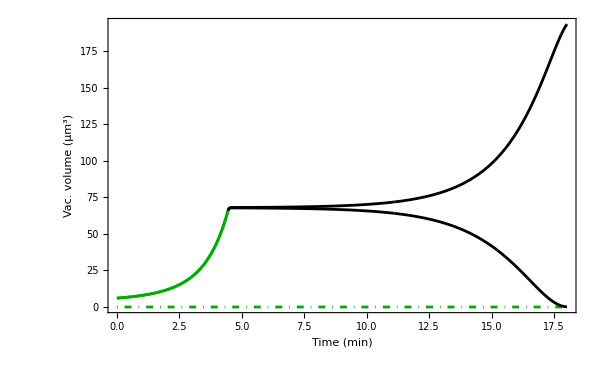

```mathematica
(*--- Plot results ---*)
rV1dat=Table[{tab[[n,1]],tab[[n,2,1]]},{n,1,Length[tab]}];
rV2dat=Table[{tab[[n,1]],tab[[n,2,2]]},{n,1,Length[tab]}];
rCdat=Table[{tab[[n,1]],tab[[n,2,3]]},{n,1,Length[tab]}];
PCdat=Table[{tab[[n,1]],tab[[n,2,4]]cf},{n,1,Length[tab]}];
ΓV1dat=Table[{tab[[n,1]],tab[[n,2,5]]},{n,1,Length[tab]}];
ΓV2dat=Table[{tab[[n,1]],tab[[n,2,6]]},{n,1,Length[tab]}];
ΓCdat=Table[{tab[[n,1]],tab[[n,2,7]]},{n,1,Length[tab]}];
ϕ1dat=Table[{tab[[n,1]],tab[[n,2,8]]},{n,1,Length[tab]}];
ϕ2dat=Table[{tab[[n,1]],tab[[n,2,9]]},{n,1,Length[tab]}];
(*F1=Table[If[flag1[[n,2]]==0,F1[[n,2]]*=(-1)],{n,1,Length[tab1]}];*)

(*--- A.1 Vacuole volume and area ---*)
vacV[x_,ϕ_]:=Module[{z},
z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;
Return[z];
]
Av[x1_,ϕ1_,x2_,ϕ2_]:=Module[{z},z=2π x1^2(1-Cos[ϕ1])+2π x2^2(1-Cos[ϕ2])+π(rE^2-2 rm^2);Return[z];]

ΑVdat=Table[{tab[[n,1]],Av[rV1dat[[n,2]],ϕ1dat[[n,2]],rV2dat[[n,2]],ϕ2dat[[n,2]]]},{n,1,Length[tab]}];
(*--- cortex-dominated regime ---*)
Α1dat1=Table[If[ΑVdat[[n,2]]≤sC,{ΑVdat[[n,1]],vacV[rV1dat[[n,2]],ϕ1dat[[n,2]]]}],{n,1,Length[tab]}];
Α1dat1=Select[Α1dat1,Length[#]==2&];
Α2dat1=Table[If[ΑVdat[[n,2]]≤sC,{ΑVdat[[n,1]],vacV[rV2dat[[n,2]],ϕ2dat[[n,2]]]}],{n,1,Length[tab]}];
Α2dat1=Select[Α2dat1,Length[#]==2&];
(*--- membrane-dominated regime ---*)
Α1dat2=Table[If[ΑVdat[[n,2]]>sC,{ΑVdat[[n,1]],vacV[rV1dat[[n,2]],ϕ1dat[[n,2]]]}],{n,1,Length[tab]}];
Α1dat2=Select[Α1dat2,Length[#]==2&];
Α2dat2=Table[If[ΑVdat[[n,2]]>sC,{ΑVdat[[n,1]],vacV[rV2dat[[n,2]],ϕ2dat[[n,2]]]}],{n,1,Length[tab]}];
Α2dat2=Select[Α2dat2,Length[#]==2&];
(*DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[ΑVdat1,Α1dat1];*)

f11=Show[(*Plot[vacV[eqsol1[[1,1]],eqsol1[[1,6]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],*)
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[Α1dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat1,Joined->True,PlotStyle->cdefault],
ListPlot[Α2dat2,Joined->True,PlotStyle->mdefault],
ListPlot[Α1dat2,Joined->True,PlotStyle->mdefault],
Frame->True,BaseStyle->bfont,PlotRange->{{t1,t2},All},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vac. volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
name11=StringJoin["volumeV.pdf"];
Export[name11,f11];
```

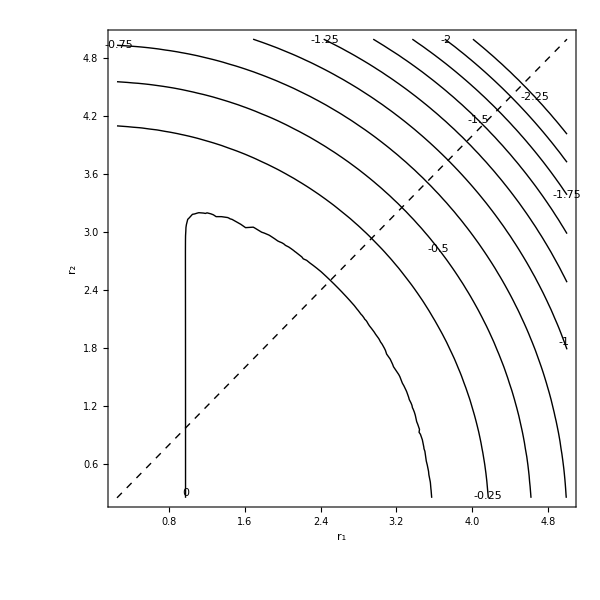

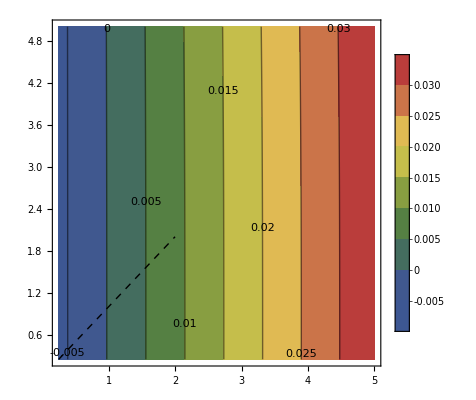

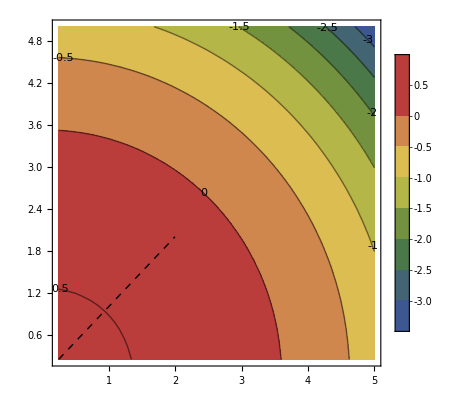

```mathematica
(*--- Contour plot ---*)
(*--- Steady-state picture ---*)
SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];

(*--- model params ---*)
γM=40;ΤC=374;
r0=10;
rm=0.25;rE=10.;
αC=0.5;
b=1.0 10^5;
ν0=2.5 10^4;
cf=0.0075;

f1[p_,r1_,r2_,x0_,a_,d_,σ0_,aC_,β_,ν_]:=Module[{σ,Σ,R,θ1,θ2,s,Σ1,s2,sC,s0,Α0,ΑC,Α,k,q,ϵ},ϵ=10^3;
(*--- other specs: additional functions ---*)
(*--- eq. 1: Cell radius ---*)
R=((x0)^3+2(r1)^3(2+Cos[θ1])(Sin[θ1/2])^4+2(r2)^3(2+Cos[θ2])(Sin[θ2/2])^4)^(1/3);
(*--- eq. 2: vacuole angles ---*)
θ1=(π-ArcSin[a/r1]);θ2=(π-ArcSin[a/r2]);
(*--- eq. 3: Limit surface tension of the cell ---*)
Α0=3π x0^2-π d^2;ΑC=Α0(1+aC);
Α=3π (R)^2-π (d)^2;
σ=Piecewise[{{σ0,Α≤ΑC},{σ0+β( Exp[(Α-ΑC)/ΑC]-1),Α>ΑC}}];
(*--- eq. 4: Limit surface tension of the vacuoles ---*)
s0=π d^2;sC=s0(1+aC);
s=2π(r1)^2(1-Cos[θ1])+2π(r2)^2(1-Cos[θ2])+π(d^2-2 a^2);
(*Σ1=Piecewise[{{σ0,s≤sC},{σ0+β(Exp[(s-sC)/sC]-1),s>sC}}];*)
Σ1=σ0+ϵ Log[1+Exp[1/ϵ(β(Exp[(s-sC)/sC]-1))]];
(*--- final result ---*)
q=r1/(4ν)(p-(2σ)/R-(2Σ1)/r1); 
Return[q]
];

(*--- dealing with the discontinuity ---*)
left[p_,r1_,r2_,x0_,a_,d_,σ0_,aC_,β_,ν_]:=Module[{σ,Σ,R,θ1,θ2,s,Σ1,s2,sC,s0,Α0,ΑC,Α,k,q},
(*--- other specs: additional functions ---*)
(*--- eq. 1: Cell radius ---*)
R=((x0)^3+2(r1)^3(2+Cos[θ1])(Sin[θ1/2])^4+2(r2)^3(2+Cos[θ2])(Sin[θ2/2])^4)^(1/3);
(*--- eq. 2: vacuole angles ---*)
θ1=(π-ArcSin[a/r1]);θ2=(π-ArcSin[a/r2]);
(*--- eq. 3: Limit surface tension of the cell ---*)
Α0=3π x0^2-π d^2;ΑC=Α0(1+aC);
Α=3π (R)^2-π (d)^2;
σ=Piecewise[{{σ0,Α≤ΑC},{σ0+β( Exp[(Α-ΑC)/ΑC]-1),Α>ΑC}}];
(*--- eq. 4: Limit surface tension of the vacuoles ---*)
s0=π d^2;sC=s0(1+aC);
s=2π(r1)^2(1-Cos[θ1])+2π(r2)^2(1-Cos[θ2])+π(d^2-2 a^2);
Σ1=σ0;
(*--- final result ---*)
q=r1/(4ν)(p-(2σ)/R-(2Σ1)/r1); 
Return[q]
];
right[p_,r1_,r2_,x0_,a_,d_,σ0_,aC_,β_,ν_]:=Module[{σ,Σ,R,θ1,θ2,s,Σ1,s2,sC,s0,Α0,ΑC,Α,k,q},
(*--- other specs: additional functions ---*)
(*--- eq. 1: Cell radius ---*)
R=((x0)^3+2(r1)^3(2+Cos[θ1])(Sin[θ1/2])^4+2(r2)^3(2+Cos[θ2])(Sin[θ2/2])^4)^(1/3);
(*--- eq. 2: vacuole angles ---*)
θ1=(π-ArcSin[a/r1]);θ2=(π-ArcSin[a/r2]);
(*--- eq. 3: Limit surface tension of the cell ---*)
Α0=3π x0^2-π d^2;ΑC=Α0(1+aC);
Α=3π (R)^2-π (d)^2;
σ=Piecewise[{{σ0,Α≤ΑC},{σ0+β( Exp[(Α-ΑC)/ΑC]-1),Α>ΑC}}];
(*--- eq. 4: Limit surface tension of the vacuoles ---*)
s0=π d^2;sC=s0(1+aC);
s=2π(r1)^2(1-Cos[θ1])+2π(r2)^2(1-Cos[θ2])+π(d^2-2 a^2);
Σ1=σ0+β(Exp[(s-sC)/sC]-1);
(*--- final result ---*)
q=r1/(4ν)(p-(2σ)/R-(2Σ1)/r1); 
Return[q]
];

Size=20;imgSize=600;imagePadding={{100,100},{80,10}};
bfont=Directive[Size,Black,FontFamily->"Arial"];
rfont=Directive[Size,Darker[Red],FontFamily->"Arial"];

pdiag=Show[ContourPlot[f1[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0],{x1,rm,5},{x2,rm,5},PlotLegends->Automatic,ContourLabels->Function[{x,y,z},Text[z,{x,y},Background->White]],
(*ColorFunction->"DarkRainbow",*)ContourShading->None,Exclusions->None],
(*DensityPlot[f1[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0]/Abs[f1[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0]],{x1,rm,5},{x2,rm,5},PlotLegends->Automatic],*)
(* add zero contour *)
(*ContourPlot[left[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0],{x1,rm,5},{x2,rm,5},Contours->{0},ContourLabels->Function[{x,y,z},Text[z,{x,y},Background->White]],ContourShading->None],
ContourPlot[right[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0],{x1,rm,5},{x2,rm,5},PlotLegends->Automatic,Contours->{0},ContourLabels->Function[{x,y,z},Text[z,{x,y},Background->White]],ContourShading->None],*)
Plot[r2,{r2,rm,5},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1]]],
Frame->True, FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},Axes->False,FrameLabel->{Style["r_1",bfont],Style["r_2",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
Export["contourplot.pdf",pdiag];
Show[ContourPlot[left[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0],{x1,rm,5},{x2,rm,5},PlotLegends->Automatic,
(*Contours->Range[-2.5,2.5,0.25],*)ContourLabels->All,ColorFunction->"DarkRainbow"],
Plot[r2,{r2,rm,2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1]]]]
Show[ContourPlot[right[7./cf,x1,x2,r0,rm,rE,γM+ΤC,αC,b,ν0],{x1,rm,5},{x2,rm,5},PlotLegends->Automatic,
(*Contours->Range[-2.5,2.5,0.25],*)ContourLabels->All,ColorFunction->"DarkRainbow"],
Plot[r2,{r2,rm,2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1]]]]
```

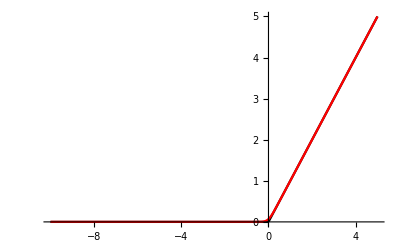

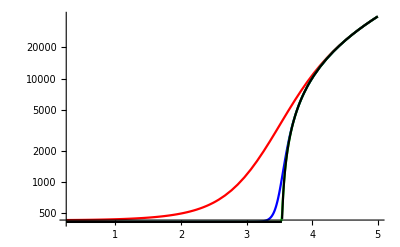

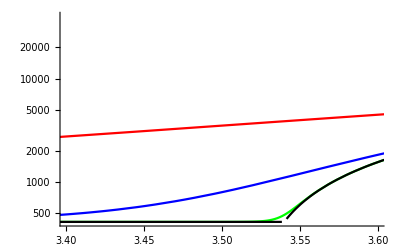

```mathematica
sigma[p_,r_,x0_,a_,d_,σ0_,aC_,β_,ν_]:=Module[{σ,Σ,R,θ,s,Σ1,s2,sC,s0,Α0,ΑC,Α,k},k=10^6;
(*--- other specs: additional functions ---*)
(*--- eq. 1: Cell radius ---*)
R=((x0)^3+2(r)^3(2+Cos[θ])(Sin[θ/2])^4)^(1/3);
(*--- eq. 2: vacuole angles ---*)
θ=(π-ArcSin[a/r]);
(*--- eq. 3: Limit surface tension of the cell ---*)
Α0=3π x0^2-π d^2;ΑC=Α0(1+aC);
Α=3π (R)^2-π (d)^2;
σ=Piecewise[{{σ0,Α≤ΑC},{σ0+β( Exp[(Α-ΑC)/ΑC]-1),Α>ΑC}}];
(*--- eq. 4: Limit surface tension of the vacuoles ---*)
s0=π d^2;sC=s0(1+aC);
s=2π(r)^2(1-Cos[θ])+π(d^2-a^2);
Σ1=Piecewise[{{σ0,s≤sC},{σ0+β(Exp[(s-sC)/sC]-1),s>sC}}];
(*Σ1=σ0+1/2(β(Exp[(s-sC)/sC]-1))(1+Tanh[k(s-sC)]);*)
(*Σ1=σ0+(Exp[1/α s/s0]-Exp[1/α]);*)
Return[Σ1]
];
sigmaApprox[p_,r_,x0_,a_,d_,σ0_,aC_,β_,ν_,ϵ_]:=Module[{σ,Σ,R,θ,s,Σ1,s2,sC,s0,Α0,ΑC,Α,k},
(*--- other specs: additional functions ---*)
(*--- eq. 1: Cell radius ---*)
R=((x0)^3+2(r)^3(2+Cos[θ])(Sin[θ/2])^4)^(1/3);
(*--- eq. 2: vacuole angles ---*)
θ=(π-ArcSin[a/r]);
(*--- eq. 3: Limit surface tension of the cell ---*)
Α0=3π x0^2-π d^2;ΑC=Α0(1+aC);
Α=3π (R)^2-π (d)^2;
σ=Piecewise[{{σ0,Α≤ΑC},{σ0+β( Exp[(Α-ΑC)/ΑC]-1),Α>ΑC}}];
(*--- eq. 4: Limit surface tension of the vacuoles ---*)
s0=π d^2;sC=s0(1+aC);
s=2π(r)^2(1-Cos[θ])+π(d^2-a^2);
(*Σ1=Piecewise[{{σ0,s≤sC},{σ0+β(Exp[(s-sC)/sC]-1),s>sC}}];*)
(*Σ1=σ0+(β(Exp[(s-sC)/sC]-1))(1/2(1+Tanh[k(s-sC)]));*)
Σ1=σ0+ϵ Log[1+Exp[1/ϵ(β(Exp[(s-sC)/sC]-1))]];
Return[Σ1]
];

e=0.1;
Show[Plot[Max[0,x],{x,-10,5},PlotStyle->Black],
Plot[e Log[1+Exp[x/e]],{x,-10,5},PlotStyle->Red],
PlotRange->All(*{{3,4},{400,10000}}*)
]
Show[LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,5 10^3],{r,0.25,5},PlotStyle->Red],
LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,10^3],{r,0.25,5},PlotStyle->Blue],
LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,10^2],{r,0.25,5},PlotStyle->Green],
LogPlot[sigma[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0],{r,0.25,5},PlotStyle->Black],PlotRange->All
]
Show[LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,5 10^3],{r,0.25,5},PlotStyle->Red],
LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,10^3],{r,0.25,5},PlotStyle->Blue],
LogPlot[sigmaApprox[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0,10^2],{r,0.25,5},PlotStyle->Green],
LogPlot[sigma[7./cf,r,r0,rm,rE,γM+ΤC,αC,b,ν0],{r,0.25,5},PlotStyle->Black],PlotRange->{{3.4,3.6},Automatic}
]
```

```mathematica
sigmaApprox[7./cf,rm,r0,rm,rE,γM+ΤC,αC,b,2.5,ν0]
```

414.

```mathematica
(*--- Legend ---*)
(*--- Output vector ---*)
(*--- (Subscript[r, V],Subscript[r, C],Subscript[P, C],σ,Σ,ϕ) ---*)
(*--- flag=0 if 0≤ϕ<π/2 ---*)
(*--- flag=1 if π/2≤ϕ≤π ---*)
(*--- Auxiliary functions ---*)
θ[r_,flag_]:=Module[{ϕ},If[flag==0,ϕ=ArcSin[rm/r],ϕ=π-ArcSin[rm/r]]; Return[ϕ];]
Av[x_,ϕ_]:=Module[{z},z=Sum[2π (x[[n]])^2(1-Cos[ϕ[[n]]]),{n,1,Length[x]}];z+=(π rE^2-Length[x] (π rm^2)); 
Return[z];]
Rc[x0_,x_,ϕ_]:=Module[{z,Α},Α=Sum[x[[n]]^3(2+Cos[ϕ[[n]]])Sin[ϕ[[n]]/2]^4,{n,1,Length[x]}];
z=(x0^3+Α)^(1/3);Return[z];]
PrintParameters[n_]:=Module[{fstream},
fstream=OpenWrite[StringJoin[Directory[],"/dataset_",ToString[n],".txt"]];
Export[fstream,StringJoin["M=",ToString[M],"\n"]];
Export[fstream,StringJoin["γM=",ToString[γM],"\n"]];
Export[fstream,StringJoin["ΤC=",ToString[ΤC],"\n"]];
Export[fstream,StringJoin["R0=",ToString[R0],"\n"]];
Export[fstream,StringJoin["rm=",ToString[rm],"\n"]];
Export[fstream,StringJoin["rE=",ToString[rE],"\n"]];
Export[fstream,StringJoin["αC=",ToString[αC],"\n"]];
Export[fstream,StringJoin["b=",ToString[b],"\n"]];
Export[fstream,StringJoin["c=",ToString[c],"\n"]];
Export[fstream,StringJoin["α=",ToString[α],"\n"]];
Export[fstream,StringJoin["Δσ=",ToString[Δσ],"\n"]];
Export[fstream,StringJoin["ΔΑ=",ToString[ΔΑ],"\n"]];
Export[fstream,StringJoin["τ0=",ToString[τ0],"\n"]];
Export[fstream,StringJoin["η0=",ToString[η0],"\n"]];
Export[fstream,StringJoin["r0=",ToString[r0],"\n"]];
Export[fstream,StringJoin["seed=",ToString[seed],"\n"]];
Close[fstream];
Return[];
]
(*--- Dynamical equations ---*)
dyn[q_,p_,x0_,y0_]:=Module[{R,t0,m,r1,r2,s1,s2,ϕ1,ϕ2,Α0,ΑC,s0,sC,flag,σ0,ϕ,y,z0,f,i,j,t,z,y1,y2,p1,p2,e1,e2,Α,σF,ΣF,η,λ,ξ,s},
(*--- 0. Initialise parameters ---*)
R={};t0=0;m=Length[y0];
r1=Table[0,{n,1,m}]; r2=Table[0,{n,1,m}];s1=Table[0,{n,1,m}]; s2=Table[0,{n,1,m}];
ϕ1=Table[0,{n,1,m}]; ϕ2=Table[0,{n,1,m}];
Α0=4π x0^2-π rE^2;ΑC=Α0(1+αC);
s0=π rE^2;sC=s0(1+αC);
(*--- 0.1 Output parameters ---*)
PrintParameters[q];
(*--- 1. Set initial condition ---*)
flag=Table[1,{n,1,m}]; σ0=Table[γM,{n,1,m}];ϕ=Table[θ[y0[[n]],flag[[n]]],{n,1,m}];
y=Rc[x0,y0,ϕ]; z0={y0,y,(2(γM+ΤC))/y,σ0,γM+ΤC,ϕ};
f=Table[If[flag[[n]]==0,-(p-Part[z0,3]-(2Part[z0,4,n])/Part[y0,n]),p-Part[z0,3]-(2Part[z0,4,n])/Part[y0,n]],{n,1,m}]; 
(*--- 2. Generate time dependent data---*)
For[i=1,i≤Length[ρ],i++,
t=ρ[[i]];
(*Print[StringJoin["t=",ToString[N[t]]]];*)
If[t==0,z=z0;AppendTo[R,{t,z,f,flag}],
r1=Part[z0,1];y1=Part[z0,2];p1=Part[z0,3];
s1=Part[z0,4]; e1=Part[z0,5]; ϕ1=Part[z0,6]; 
(*Print[StringJoin["s0=",ToString[N[s0]]]];*)
(*--- 3. Auxiliary functions ---*)
(*--- 3.1 Force exerted on the vacuole ---*)
f=Table[If[flag[[n]]==0,-(p-p1-(2s1[[n]])/r1[[n]]),p-p1-(2s1[[n]])/r1[[n]]],{n,1,m}];
(*--- 3.2 Surface tensions ---*)
Α=4π y1^2-π rE^2; s=Av[r1,ϕ1];If[Α≤ΑC,σF=γM+ΤC+Δσ/ΔΑ(Α/Α0-1)^α,σF=γM+ΤC+Δσ+b( Exp[(Α-ΑC)/ΑC]-1)];If[s≤sC,ΣF=γM+ΤC+Δσ/ΔΑ(s/s0-1)^α,ΣF=γM+ΤC+Δσ+b( Exp[(s-sC)/sC]-1)];
(*--- 3.3 Drag coefficient ---*)
η=4η0;(*If[Α≤Α0(1+αC),η=η0,η=η0 Exp[(Α-ΑC)/ΑC]];*)
(*--- 3.4 Tension growth timescale ---*)
If[s≤sC,λ=τ0,λ=0];
If[Α≤ΑC,ξ=τ0,ξ=0];
(*--- 4. Dynamical equations ---*)
For[j=1,j≤m,j++,
r2[[j]]=r1[[j]]+r1[[j]]/η f[[j]] Δt;
If[λ≠0,s2[[j]]=s1[[j]]-1/λ(s1[[j]]-ΣF)Δt,s2[[j]]=ΣF];
If[ξ≠0,e2=e1-1/ξ(e1 -σF)Δt,e2=σF];
(*Print[StringJoin["s2=",ToString[N[{h2,s2,e2}]]]];*)
(*--- 5. Check configuration ---*)
If[r2[[j]]≤rm,
(*--- Angle switch ---*)
If[flag[[j]]==0,flag[[j]]=1,flag[[j]]=0];i--;
Break[]
,
(*--- Configuration accepted ---*) 
ϕ2[[j]]=θ[r2[[j]],flag[[j]]]; 
];
];

(*--- 6. Calculate new configuration ---*)
If[j==m+1,y2=Rc[x0,r2,ϕ2];p2=(2e2)/y2;z={r2,y2,p2,s2,e2,ϕ2};
AppendTo[R,{t,z,f,flag}];z0=z;
];
];
];
Return[R];
];

(*Print[StringJoin["flag=",ToString[flag]]];
Print[StringJoin["s=",ToString[N[s]]]];*)
(*AppendTo[R,{t,s,f}];s0=s;*)
(*If[First[s]==0,s0=sflat,s0=s];*)
(*If[First[s0]≥xC,flag=1,flag=0];*)
```

SetDirectory::cdir: Cannot set current directory to /Users/cairoliandrea/Desktop/WORK/Projects-Chiu-Fan/Project-Glaucoma/data/kinetic.

```mathematica
(*--- Generate data ---*)
date=DateString[{"Year","_","Month","_","Day"}];
(*--- Membrane dominated phase ---*)
indx=1;M=2;
r0=RandomVariate[UniformDistribution[{rm,1.2rm}],M];
dat1=dyn[indx,8/cf,R0,r0]; Export[StringJoin["dat_",ToString[indx],".txt"],dat1,"Table"];
(*--- Mixed phase ---*)
indx=2;M=2;
r0=RandomVariate[UniformDistribution[{rm,1.2rm}],M];
dat2=dyn[indx,2/cf,R0,r0];
Export[StringJoin["dat_",ToString[indx],".txt"],dat2,"Table"];
(*indx=3;r0=RandomVariate[UniformDistribution[{rm,1.2rm}],M];
dat3=dyn[indx,2/cf,R0,r0];Export[StringJoin["dat_",ToString[indx],".txt"],dat3,"Table"];*)
(*--- Three vacuoles case ---*)
indx=3; M=3;
r0=RandomVariate[UniformDistribution[{rm,1.2rm}],M];dat4=dyn[indx,8/cf,R0,r0];Export[StringJoin["dat_",ToString[indx],".txt"],dat4,"Table"];

tconv=60;
t1=t1/tconv; t2=t2/tconv;
```

```mathematica
(*--- Manage data ---*)
M=2;
tab1=Table[{dat1[[n,1]]/tconv,dat1[[n,2]]},{n,1,Length[ρ]}];
flag1=Table[{dat1[[n,1]]/tconv,dat1[[n,4]]},{n,1,Length[ρ]}];
F1=Table[{dat1[[n,1]]/tconv,dat1[[n,3]]},{n,1,Length[ρ]}];
F1=Table[{F1[[n,1]],F1[[n,2,m]]},{m,1,M},{n,1,Length[ρ]}];
Table[If[flag1[[n,2,m]]==0,F1[[m,n,2]]*=-1],{m,1,M},{n,1,Length[ρ]}];

M=2;
tab2=Table[{dat2[[n,1]]/tconv,dat2[[n,2]]},{n,1,Length[ρ]}];
flag2=Table[{dat2[[n,1]]/tconv,dat2[[n,4]]},{n,1,Length[ρ]}];
F2=Table[{dat2[[n,1]]/tconv,dat2[[n,3]]},{n,1,Length[ρ]}];
F2=Table[{F2[[n,1]],F2[[n,2,m]]},{m,1,M},{n,1,Length[ρ]}];
Table[If[flag2[[n,2,m]]==0,F2[[m,n,2]]*=-1],{m,1,M},{n,1,Length[ρ]}];

(*M=2;
tab3=Table[{dat3[[n,1]]/tconv,dat3[[n,2]]},{n,1,Length[ρ]}];
flag3=Table[{dat3[[n,1]]/tconv,dat3[[n,4]]},{n,1,Length[ρ]}];
F3=Table[{dat3[[n,1]]/tconv,dat3[[n,3]]},{n,1,Length[ρ]}];
F3=Table[{F3[[n,1]],F3[[n,2,m]]},{m,1,M},{n,1,Length[ρ]}];
Table[If[flag3[[n,2,m]]==0,F3[[m,n,2]]*=-1],{m,1,M},{n,1,Length[ρ]}];*)

M=3;
tab4=Table[{dat4[[n,1]]/tconv,dat4[[n,2]]},{n,1,Length[ρ]}];
flag4=Table[{dat4[[n,1]]/tconv,dat4[[n,4]]},{n,1,Length[ρ]}];
F4=Table[{dat4[[n,1]]/tconv,dat4[[n,3]]},{n,1,Length[ρ]}];
F4=Table[{F4[[n,1]],F4[[n,2,m]]},{m,1,M},{n,1,Length[ρ]}];
Table[If[flag4[[n,2,m]]==0,F4[[m,n,2]]*=-1],{m,1,M},{n,1,Length[ρ]}];

(*tab5=Table[{dat5[[n,1]]/tconv,dat5[[n,2]]},{n,1,Length[ρ]}];
F5=Table[{dat5[[n,1]]/tconv,dat5[[n,3]]},{n,1,Length[ρ]}];*)
```

```mathematica
(*--- Function for plotting numerical results ---*)
areaV[x_,ϕ_]:=Module[{z},z=2π x^2(1-Cos[ϕ]); Return[z];]
vacV[x_,ϕ_]:=Module[{z},z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;Return[z];]
GenerateResults[indx_,tab_,F_,eqsol_,t_,Α_,ψ_,p_,ΓV_,ΓC_,f_,control_]:=Module[{rVdat,rCdat,PCdat,ΓVdat,ΓCdat,ϕdat,ΑVdat,ΑCdat,Αtot,Α1dat,Α2dat,name1,f1,ϕ1dat,ϕ2dat,f2,name2,PC1dat,PC2dat,f3,name3,ΓV1dat,ΓV2dat,f4,name4,ΓC1dat,ΓC2dat,f5,name5,F1,F2,f6,name6,l1style,l2style,Α0,ΑC,s0,sC},
Α0=4π R0^2-π rE^2;ΑC=Α0(1+αC);
s0=π rE^2;sC=s0(1+αC);
(*--- Line color for eq. solution ---*)
If[areaV[eqsol[[1]],eqsol[[6]]]+π(rE^2-rm^2)≤sC,l1style=cdefault,l1style=mdefault];
If[4π (eqsol[[2]])^2-π rE^2≤ΑC,l2style=cdefault,l2style=mdefault];

(*--- 1. Tables engine ---*)
rVdat=Table[{tab[[n,1]],tab[[n,2,1,m]]},{m,1,M},{n,1,Length[tab]}];
rCdat=Table[{tab[[n,1]],tab[[n,2,2]]},{n,1,Length[tab]}];
PCdat=Table[{tab[[n,1]],tab[[n,2,3]]cf},{n,1,Length[tab]}];
ΓVdat=Table[{tab[[n,1]],tab[[n,2,4,m]]},{m,1,M},{n,1,Length[tab]}];
ΓCdat=Table[{tab[[n,1]],tab[[n,2,5]]},{n,1,Length[tab]}];
ϕdat=Table[{tab[[n,1]],tab[[n,2,6,m]]},{m,1,M},{n,1,Length[tab]}];

(*--- 1.1 Calculate areas ---*)
ΑVdat=Table[{tab[[n,1]],Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]},{n,1,Length[tab]}];
(*Αtot=Table[ΑCdat[[n,2]]+Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]-π rm^2,{n,1,Length[tab]}];*)

(*--- 1.2 Highlight different regimes ---*)
Α1dat=Table[If[ΑVdat[[n,2]]≤sC,{ΑVdat[[n,1]],vacV[rVdat[[m,n,2]],ϕdat[[m,n,2]]]}],{m,1,M},{n,1,Length[tab]}];
Α2dat=Table[If[ΑVdat[[n,2]]>sC,{ΑVdat[[n,1]],vacV[rVdat[[m,n,2]],ϕdat[[m,n,2]]]}],{m,1,M},{n,1,Length[tab]}];

(*--- A.1 Vacuole area ---*)
Print["1. Vacuole volume"];
f1=Show[Plot[vacV[eqsol[[1]],eqsol[[6]]],{x,t1,t2},PlotStyle->{l1style,DotDashed}],
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Table[ListPlot[Α1dat[[m]],Joined->True,PlotStyle->cdefault],{m,1,M}],
Table[ListPlot[Α2dat[[m]],Joined->True,PlotStyle->mdefault],{m,1,M}],
Frame->True,BaseStyle->bfont,PlotRange->{t,Α},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vacuole volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding];
name1=StringJoin["volumeV_",ToString[indx],".pdf"];
Export[name1,f1];Print[f1];

If[control==1,Return[]];

(*zoom1=Show[Plot[area[eqsol1[[2,1]],eqsol1[[2,5]]],{x,t1,t2},PlotStyle->{mdefault,DotDashed}],
Plot[π rm^2,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Table[ListPlot[Α1dat1[[m]],Joined->True,PlotStyle->cdefault],{m,1,M}],
Table[ListPlot[Α2dat1[[m]],Joined->True,PlotStyle->mdefault],{m,1,M}],
Frame->True,BaseStyle->bfont,PlotRange->{{2,5},{800,1200}},FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["Vacuole area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
*)(*nameZ1=StringJoin["zoom1_",ToString[date],".pdf"];
Export[nameZ1,zoom1];*)

(*--- A.2 Vacuole geometry ---*)
Print["2. Vacuole angle"];
ϕ1dat=Table[If[ΑVdat[[n,2]]≤sC,ϕdat[[m,n]]],{m,1,M},{n,1,Length[tab]}];
ϕ2dat=Table[If[ΑVdat[[n,2]]>sC,ϕdat[[m,n]]],{m,1,M},{n,1,Length[tab]}];

f2=Show[Plot[eqsol[[6]],{x,t1,t2},PlotStyle->{l1style,DotDashed}],
Table[ListPlot[ϕ1dat[[m]],Joined->True,PlotStyle->cdefault],{m,1,M}],
Table[ListPlot[ϕ2dat[[m]],Joined->True,PlotStyle->mdefault],{m,1,M}],
PlotRange->{t,ψ},Frame->True,BaseStyle->bfont,
FrameTicks->{{{0,π/4,π/2,3π/4,π},{0,π/4,π/2,3π/4,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Time (min)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding];
name2=StringJoin["phi_",ToString[indx],".pdf"];
Export[name2,f2];Print[f2];

If[control==2,Return[]];

(*--- A.3 Intracellular pressure ---*)
Print["3. Intracellular pressure"];
PC1dat=Table[If[ΑVdat[[n,2]]≤sC,{PCdat[[n,1]],PCdat[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab]}];
PC2dat=Table[If[ΑVdat[[n,2]]>sC,{PCdat[[n,1]],PCdat[[n,2]]-(2(γM+ΤC)/R0) cf}],{n,1,Length[tab]}];

f3=Show[Plot[(eqsol[[3]]-(2(γM+ΤC)/R0))cf,{x,t1,t2},PlotStyle->{l1style,DotDashed}],
Plot[0,{x,t1,t2},PlotRange->All,PlotStyle->{cdefault,DotDashed}],
ListPlot[PC1dat,Joined->True,PlotStyle->cdefault],
ListPlot[PC2dat,Joined->True,PlotStyle->mdefault],
PlotRange->{t,p},
Frame->True,BaseStyle->bfont,FrameTicksStyle->{Automatic,Automatic},FrameLabel->{Style["Time (min)",bfont],Style["P-P_0 (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding];
name3=StringJoin["press_",ToString[indx],".pdf"];
Export[name3,f3];Print[f3];

If[control==3,Return[]];

(*--- A.4 Vacuole/Cell surface tension ---*)
Print["4. Vacuole surface tension"];
ΓV1dat=Table[If[ΑVdat[[n,2]]≤sC,{ΓVdat[[m,n,1]],ΓVdat[[m,n,2]]-(γM+ΤC)}],{m,1,M},{n,1,Length[tab]}];
ΓV2dat=Table[If[ΑVdat[[n,2]]>sC,{ΓVdat[[m,n,1]],ΓVdat[[m,n,2]]-(γM+ΤC)}],{m,1,M},{n,1,Length[tab]}];

f4=Show[Plot[eqsol[[4]]-(γM+ΤC),{x,t1,t2},PlotStyle->{l1style,DotDashed}],
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
Table[ListPlot[ΓV1dat[[m]],Joined->True,PlotStyle->cdefault],{m,1,M}],
Table[ListPlot[ΓV2dat[[m]],Joined->True,PlotStyle->mdefault],{m,1,M}],
PlotRange->{t,ΓV},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["Time (min)",bfont],Style["Σ-σ_0 (pN/μm)",bfont]},
FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding];
name4=StringJoin["tensionV_",ToString[indx],".pdf"];
Export[name4,f4];Print[f4];

If[control==4,Return[]];

Print["5. Cell surface tension"];
ΑCdat=Table[{tab[[n,1]],4π (rCdat[[n,2]])^2-π rE^2},{n,1,Length[tab]}];

ΓC1dat=Table[If[ΑCdat[[n,2]]≤ΑC,{ΓCdat[[n,1]],ΓCdat[[n,2]]-(γM+ΤC)}],{n,1,Length[tab]}];
ΓC2dat=Table[If[ΑCdat[[n,2]]>ΑC,{ΓCdat[[n,1]],ΓCdat[[n,2]]-(γM+ΤC)}],{n,1,Length[tab]}];

f5=Show[Plot[eqsol[[5]]-(γM+ΤC),{x,t1,t2},PlotStyle->{l2style,DotDashed}],
Plot[0,{x,t1,t2},PlotStyle->{cdefault,DotDashed}],
ListPlot[ΓC1dat,Joined->True,PlotStyle->cdefault],
ListPlot[ΓC2dat,Joined->True,PlotStyle->mdefault],
PlotRange->{t,ΓC},Frame->True,BaseStyle->bfont,
FrameTicksStyle->{bfont,bfont},FrameLabel->{Style["Time (min)",bfont],Style["σ-σ_0 (pN/μm)",bfont]},
FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding];
name5=StringJoin["tensionC_",ToString[indx],".pdf"];
Export[name5,f5];Print[f5];

If[control==5,Return[]];

(*--- A.5 Force on vacuole ---*)
Print["6. Force on vacuole"];
F1=Table[If[ΑVdat[[n,2]]≤sC,F[[m,n]]],{m,1,M},{n,1,Length[tab]}];
F2=Table[If[ΑVdat[[n,2]]>sC,F[[m,n]]],{m,1,M},{n,1,Length[tab]}];

f6=Show[Plot[0,{x,t1,t2},PlotStyle->{l1style,DotDashed}],
Table[ListPlot[F1[[m]],Joined->True,PlotStyle->cdefault],{m,1,2}],
Table[ListPlot[F2[[m]],Joined->True,PlotStyle->mdefault],{m,1,2}],
PlotRange->{t,f},Frame->True,BaseStyle->bfont,Axes->False,
FrameTicksStyle->{Directive[bfont,FontFamily->"Arial"],bfont},
FrameLabel->{Style["Time (min)",bfont],Style["Force (pN/μm)",bfont]},FrameStyle->{{bfont,bfont},{bfont,bfont}},ImageSize->imgSize,ImagePadding->imagePadding];
name6=StringJoin["force_",ToString[indx],".pdf"];
Export[name6,f6];Print[f6];

If[control==6,Return[]];

Return[]

]
```

1. Vacuole volume

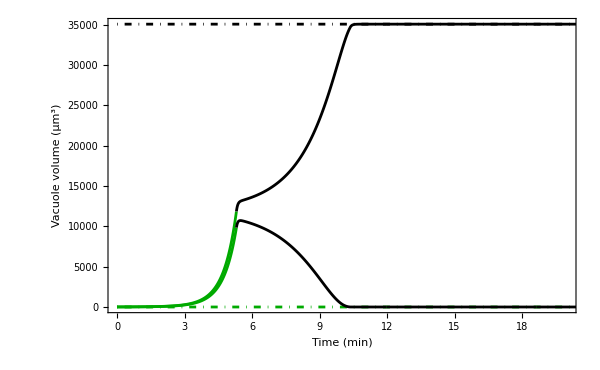

2. Vacuole angle

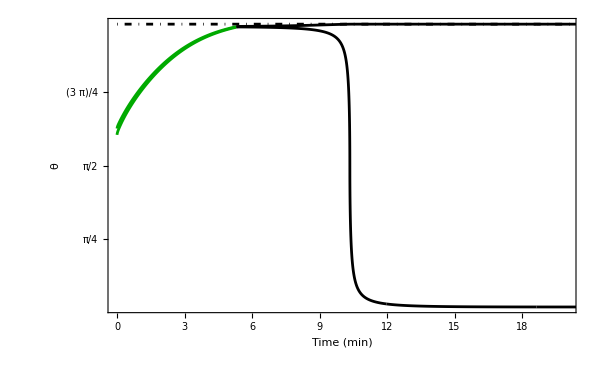

3. Intracellular pressure

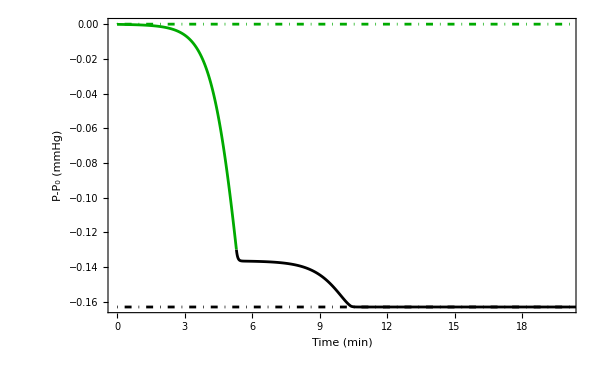

4. Vacuole surface tension

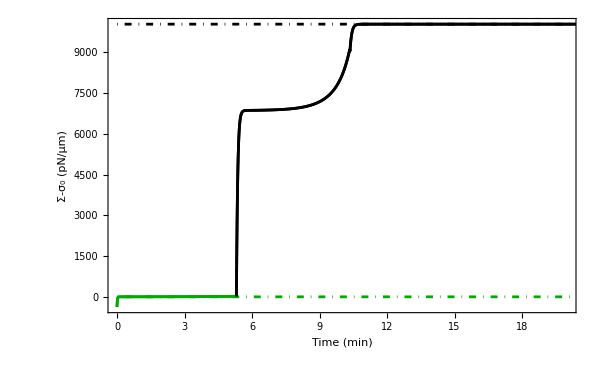

5. Cell surface tension

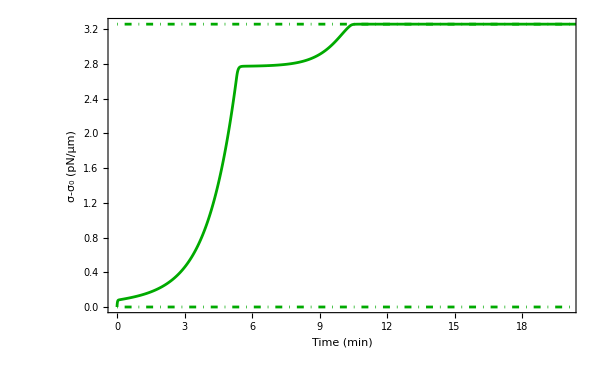

6. Force on vacuole

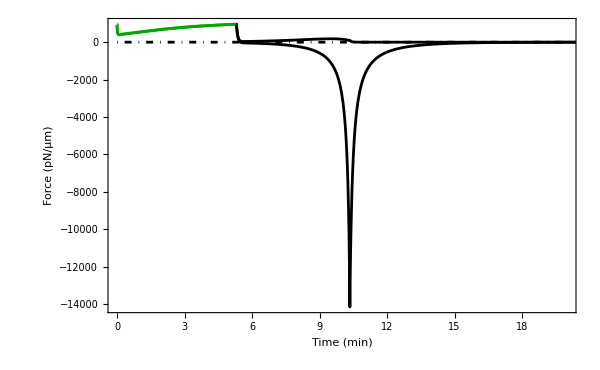

```mathematica
(*--- Simulation 1 ---*)
eqsol1={20.30190566258055,22.314866422266473,37.39723186999805,10448.065483309787,417.25711687076654,3.079983110653228};
indx=1;M=2;results=tab1;force=F1;sol=eqsol1;
GenerateResults[indx,results,force,sol,{0,20},All,All,All,All,All,All,0]
```

```mathematica
(*--- Simulation 4 ---*)
eqsol1={20.30190566258055,22.314866422266473,37.39723186999805,10448.065483309787,417.25711687076654,3.079983110653228};
(*{{3.4248561724806095,25.000533553741445,33.133598395779885,414.17881922494433,0.6236058846443161},{3.481745538692024,25.021969233348887,33.59141188430261,420.26163733688503,2.529691724142795},{12.158681328038925,25.923945299206753,87.7995469676604,1138.055326442381,2.976350164109458}};*)
indx=4;M=3;results=tab4;force=F4;sol=eqsol1;
GenerateResults[indx,results,force,sol,{0,20},All,All,All,All,All,All,0];
```

1. Vacuole volume

-Graphics-

2. Vacuole angle

-Graphics-

3. Intracellular pressure

-Graphics-

4. Vacuole surface tension

-Graphics-

5. Cell surface tension

-Graphics-

6. Force on vacuole

-Graphics-

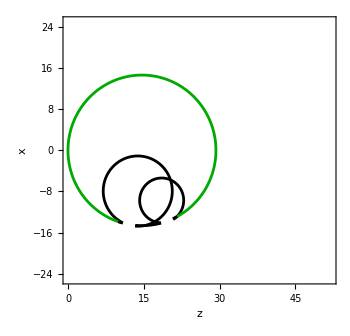

```mathematica
(*--- Animations ---*)
(* Two blebs case *)
(*--- Auxiliary functions ---*)
Clear[x,y,z];
x[r_,ψ_,ϕ_,f_]:=Module[{},Return[r Cos[ψ]Sin[θ[r,f]-ϕ]];]
y[r_,ψ_,ϕ_,f_]:=Module[{},Return[r Sin[ψ]Sin[θ[r,f]-ϕ]];]
z[r_,ϕ_,f_]:=Module[{},Return[r Cos[θ[r,f]-ϕ]-r Cos[θ[r,f]]];]

(*--- Generate 2D frames ---*)
(*--- 1 frame ---*)
Frame2D[tab_,flag_,j_,l1_,l2_]:=Module[{fig,style1,style2,m,xC,Μ1,ψ1,ϕ1,Μ2,ψ2,ϕ2,rVdat,rCdat,ϕdat,ΑVdat,ΑCdat,Αtot,Α0,ΑC,s0,sC},
Α0=4π R0^2-π rE^2;ΑC=Α0(1+αC);
s0=π rE^2;sC=s0(1+αC);

(*--- 1. Tables engine ---*)
rVdat=Table[{tab[[n,1]],tab[[n,2,1,m]]},{m,1,M},{n,1,Length[tab]}];
rCdat=Table[{tab[[n,1]],tab[[n,2,2]]},{n,1,Length[tab]}];
ϕdat=Table[{tab[[n,1]],tab[[n,2,6,m]]},{m,1,M},{n,1,Length[tab]}];

(*--- 1.1 Calculate areas ---*)
ΑVdat=Table[{tab[[n,1]],Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]},{n,1,Length[tab]}];
ΑCdat=Table[{tab[[n,1]],4π (rCdat[[n,2]])^2-π rE^2},{n,1,Length[tab]}];
(*Αtot=Table[ΑCdat[[n,2]]+Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]-π rm^2,{n,1,Length[tab]}];*)

(*--- Choose color ---*)
If[ΑVdat[[j,2]]≤sC,style1=cdefault,style1=mdefault];
If[ΑCdat[[j,2]]≤ΑC,style2=cdefault,style2=mdefault];
fig=Show[
(* Plot first bleb *)
m=1;  ψ1=(5π)/12; ϕ1=ArcSin[rVdat[[m,j,2]]/rCdat[[j,2]] Sin[ϕdat[[m,j,2]]]];
Μ1={{Cos[ψ1],-Sin[ψ1]},{Sin[ψ1],Cos[ψ1]}};
xC={z[rCdat[[j,2]],ψ1,1],x[rCdat[[j,2]],0,π+ψ1,1]}; 
ParametricPlot[xC+Μ1.{z[rVdat[[m,j,2]],s,flag[[j,2,m]]],x[rVdat[[m,j,2]],0,s,flag[[j,2,m]]]},{s,0,2ϕdat[[m,j,2]]},PlotStyle->style1],
(* Plot second bleb *)
m=2;  ψ2=(7π)/12; xC={z[rCdat[[j,2]],ψ2,1],x[rCdat[[j,2]],0,π+ψ2,1]}; Μ2={{Cos[ψ2],-Sin[ψ2]},{Sin[ψ2],Cos[ψ2]}};
ϕ2=ArcSin[rVdat[[m,j,2]]/rCdat[[j,2]] Sin[ϕdat[[m,j,2]]]];
ParametricPlot[xC+Μ2.{z[rVdat[[m,j,2]],s,flag[[j,2,m]]],x[rVdat[[m,j,2]],0,s,flag[[j,2,m]]]},{s,0,2ϕdat[[m,j,2]]},PlotStyle->style1],
(* Plot cell *)
ParametricPlot[{z[rCdat[[j,2]],s,1],x[rCdat[[j,2]],0,s,1]},{s,-ψ1-ϕ1,2π-ψ2-3ϕ2},PlotStyle->style2],
ParametricPlot[{z[rCdat[[j,2]],s,1],x[rCdat[[j,2]],0,s,1]},{s,-ψ1-ϕ1+π/48,-ψ1-ϕ1},PlotStyle->style1],
ParametricPlot[{z[rCdat[[j,2]],s,1],x[rCdat[[j,2]],0,s,1]},{s,2π-ψ2-3ϕ2-π/48,2π-ψ2-3ϕ2},PlotStyle->style1],
ParametricPlot[{z[rCdat[[j,2]],s,1],x[rCdat[[j,2]],0,s,1]},{s,2π-3ϕ1-ψ1,2π-ψ2-ϕ2},PlotStyle->style1],
(* Figure specs *)
Frame->True, FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},Axes->False,FrameLabel->{Style["z",bfont],Style["x",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding,PlotRange->{l1,l2}];
Return[fig];
]

(*--- Table of frames ---*)
Frame2DEngine[tab_,flag_,tI_,tF_,tS_,l1_,l2_]:=Module[{style1,style2,i,f,xC,Μ1,ψ1,ϕ1,Μ2,ψ2,ϕ2,rVdat,rCdat,ϕdat,ΑVdat,ΑCdat,Αtot,res,Α0,ΑC,s0,sC},
Α0=4π R0^2-π rE^2;ΑC=Α0(1+αC);
s0=π rE^2;sC=s0(1+αC);

(*--- 1. Tables engine ---*)
rVdat=Table[{tab[[n,1]],tab[[n,2,1,m]]},{m,1,M},{n,1,Length[tab]}];
rCdat=Table[{tab[[n,1]],tab[[n,2,2]]},{n,1,Length[tab]}];
ϕdat=Table[{tab[[n,1]],tab[[n,2,6,m]]},{m,1,M},{n,1,Length[tab]}];

(*--- 1.1 Calculate areas ---*)
ΑVdat=Table[{tab[[n,1]],Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]},{n,1,Length[tab]}];
ΑCdat=Table[{tab[[n,1]],4π (rCdat[[n,2]])^2-π rE^2},{n,1,Length[tab]}];
(*Αtot=Table[ΑCdat[[n,2]]+Av[rVdat[[;;,n,2]],ϕdat[[;;,n,2]]]-π rm^2,{n,1,Length[tab]}];*)

i=Position[ρ,SelectFirst[ρ,#1≥tI &]][[1,1]];
f=Position[ρ,SelectFirst[ρ,#1>tF &]]; If[Length[f]==0,f=Length[ρ],f=f[[1,1]]]; 
(*--- Frame engine ---*)
res=ParallelTable[
(*--- Choose color ---*)
If[ΑVdat[[n,2]]≤sC,style1=cdefault,style1=mdefault];
If[ΑCdat[[n,2]]≤ΑC,style2=cdefault,style2=mdefault];
(*--- Generate frame ---*)
Show[
(* Plot first bleb *)
m=1;  ψ1=(5π)/12; ϕ1=ArcSin[rVdat[[m,n,2]]/rCdat[[n,2]] Sin[ϕdat[[m,n,2]]]];
Μ1={{Cos[ψ1],-Sin[ψ1]},{Sin[ψ1],Cos[ψ1]}};
xC={z[rCdat[[n,2]],ψ1,1],x[rCdat[[n,2]],0,π+ψ1,1]}; 
ParametricPlot[xC+Μ1.{z[rVdat[[m,n,2]],s,flag[[n,2,m]]],x[rVdat[[m,n,2]],0,s,flag[[n,2,m]]]},{s,0,2ϕdat[[m,n,2]]},PlotStyle->style1],
(* Plot second bleb *)
m=2;  ψ2=(7π)/12; xC={z[rCdat[[n,2]],ψ2,1],x[rCdat[[n,2]],0,π+ψ2,1]}; Μ2={{Cos[ψ2],-Sin[ψ2]},{Sin[ψ2],Cos[ψ2]}};
ϕ2=ArcSin[rVdat[[m,n,2]]/rCdat[[n,2]] Sin[ϕdat[[m,n,2]]]];
ParametricPlot[xC+Μ2.{z[rVdat[[m,n,2]],s,flag[[n,2,m]]],x[rVdat[[m,n,2]],0,s,flag[[n,2,m]]]},{s,0,2ϕdat[[m,n,2]]},PlotStyle->style1],
(* Plot cell *)
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,-ψ1-ϕ1,2π-ψ2-3ϕ2},PlotStyle->style2],
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,-ψ1-ϕ1+π/48,-ψ1-ϕ1},PlotStyle->style1],
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,2π-ψ2-3ϕ2-π/48,2π-ψ2-3ϕ2},PlotStyle->style1],
ParametricPlot[{z[rCdat[[n,2]],s,1],x[rCdat[[n,2]],0,s,1]},{s,2π-3ϕ1-ψ1,2π-ψ2-ϕ2},PlotStyle->style1],
Frame->True, FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},Axes->False,FrameLabel->{Style["z",bfont],Style["x",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding,PlotRange->{l1,l2}],{n,i,f,tS}];
Return[res];
]

(*--- Plot 2D ---*)
Size=20;imgSize=350;imagePadding={{70,20},{60,2}};
(*--- Exemplary frame ---*)
indx=1;M=2;data=tab1;fdata=flag1;
fig1=Frame2D[data,fdata,5000,{0,52},{-25,25}]
(*For[i=1,i≤12,i++,fig2=Frame2D[data,fdata,1+(i-1)*(60/Δt),{0,52},{-25,25}];Export[StringJoin["Frame_",ToString[i],".pdf"],fig2]];
frames2D1=Frame2DEngine[data,fdata,0 60,10 60,50,{0,52},{-25,25}];
Export["movie2D1.avi",frames2D1];*)
(*fig2=Frame2D[rVdat4,rCdat4,ϕdat4,flag4,{0,45},{-25,25}]*)
(*frames2D2=Frame2DEngine[rVdat4,rCdat4,ϕdat4,flag4,30 60,50,{0,45},{-25,25}];*)
```

```mathematica
(*(*--- Animation ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/kinetic/",date]];
If[DirectoryQ["movies"]==False,CreateDirectory["movies"]];SetDirectory["movies"];
(*--- Movie 1 ---*)
If[DirectoryQ["movie2D_1"]==False,CreateDirectory["movie2D_1"]]; SetDirectory["movie2D_1"];
movie2D1=ListAnimate[frames2D1,AnimationRepetitions->1];
Export["frame001.png",frames2D1,"VideoFrames"];
(*(*--- Movie 2 ---*)
SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/dynamics/",date,"/movies"]];If[DirectoryQ["movie2D_2"]==False,CreateDirectory["movie2D_2"]]; SetDirectory["movie2D_2"];
movie2D2=ListAnimate[frames2D2,AnimationRepetitions->1];
Export["frame001.png",frames2D2,"VideoFrames"];
*)SetDirectory[StringJoin["/home/ac6411/Desktop/MyProjects/Project-Chiu-Fan/Project-Glaucoma/data/kinetic/",date]];*)
```

```mathematica
(*(*--- Plot 3D ---*)
(*--- Generate frames ---*)
(*--- 1 frame ---*)
Frame3D[rVdat_,rCdat_,ϕdat_,flag_,l1_,l2_,l3_]:=Module[{fig,n},n=Length[ρ];fig=Show[ParametricPlot3D[{x[rVdat[[n,2]]/rm,ϕ,s,flag[[n,2]]],y[rVdat[[n,2]]/rm,ϕ,s,flag[[n,2]]],z[rVdat[[n,2]]/rm,s,flag[[n,2]]]},{ϕ,-π/8,3π/2},{s,0,ϕdat[[n,2]]},PlotStyle->{LightGray},Mesh->None],
ParametricPlot3D[{x[rCdat[[n,2]]/rm,ϕ,s,1],y[rCdat[[n,2]]/rm,ϕ,s,1],z[rCdat[[n,2]]/rm,s,1]},{ϕ,-π/8,3π/2},{s,0,π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]]},PlotStyle->{Green},Mesh->None],
PlotRange->{l1,l2,l3},AxesLabel->{"x","y","z"},LabelStyle->{bfont},Frame->True,PlotRangeClipping->False];
Return[fig];
]
(*--- Table of frames ---*)
Frame3DEngine[rVdat_,rCdat_,ϕdat_,flag_,tF_,tS_,l1_,l2_,l3_]:=Module[{tab,t},t=Select[ρ,#<tF&];
tab=ParallelTable[Show[
ParametricPlot3D[{x[rVdat[[n,2]]/rm,ϕ,s,flag[[n,2]]],y[rVdat[[n,2]]/rm,ϕ,s,flag[[n,2]]],z[rVdat[[n,2]]/rm,s,flag[[n,2]]]},{ϕ,-π/8,3π/2},{s,0,ϕdat[[n,2]]},PlotStyle->{LightGray},Mesh->None],
ParametricPlot3D[{x[rCdat[[n,2]]/rm,ϕ,s,1],y[rCdat[[n,2]]/rm,ϕ,s,1],z[rCdat[[n,2]]/rm,s,1]},{ϕ,-π/8,3π/2},{s,0,π-ArcSin[rVdat[[n,2]]/rCdat[[n,2]] Sin[ϕdat[[n,2]]]]},PlotStyle->{Green},Mesh->None],
PlotRange->{l1,l2,l3},AxesLabel->{"x","y","z"},LabelStyle->{bfont},Frame->True,PlotRangeClipping->False],{n,1,Length[t],tS}];
Return[tab];
]

(*--- Exemplary frame ---*)
fig1=Frame3D[rVdat1,rCdat1,ϕdat1,flag1,{-25,25},{-25,25},{0,45}]
fig2=Frame3D[rVdat4,rCdat4,ϕdat4,flag4,{-25,25},{-25,25},{0,45}]
frames3D1=Frame3DEngine[rVdat1,rCdat1,ϕdat1,flag1,10 60,10,{-25,25},{-25,25},{0,45}];
frames3D2=Frame3DEngine[rVdat4,rCdat4,ϕdat4,flag4,30 60,50,{-25,25},{-25,25},{0,45}];
(*--- Animation ---*)
Export["movie3D1.avi",frames3D1];
Export["movie3D2.avi",frames3D2];
*)
```

-Graphics3D-

-Graphics3D-

```mathematica
(*(*--- Animation ---*)
ListAnimate[Table[Show[frames3D[[n]],PlotStyle->bdefault],{n,1,Length[frames3D]}]]*)
```